```mathematica
SetDirectory[NotebookDirectory[]]
rasterizeBackground[g_,res_: 100]:=Show[Graphics[{Inset[Rasterize[Show[g,ImagePadding->0,ImageMargins->0,LabelStyle->Opacity[0],FrameTicksStyle->Opacity[0],FrameStyle->Opacity[0],AxesStyle->Opacity[0],TicksStyle->Opacity[0],PlotRangeClipping->False],ImageResolution->res],Scaled[{0,0}],Scaled[{0,0}],Scaled[1]]}],Sequence@@Options[g],Sequence@@AbsoluteOptions[g,PlotRange],Sequence@@Options[g,Epilog]]
```

/home/zack/cantera/ratematrix

test

{100.,9,27}

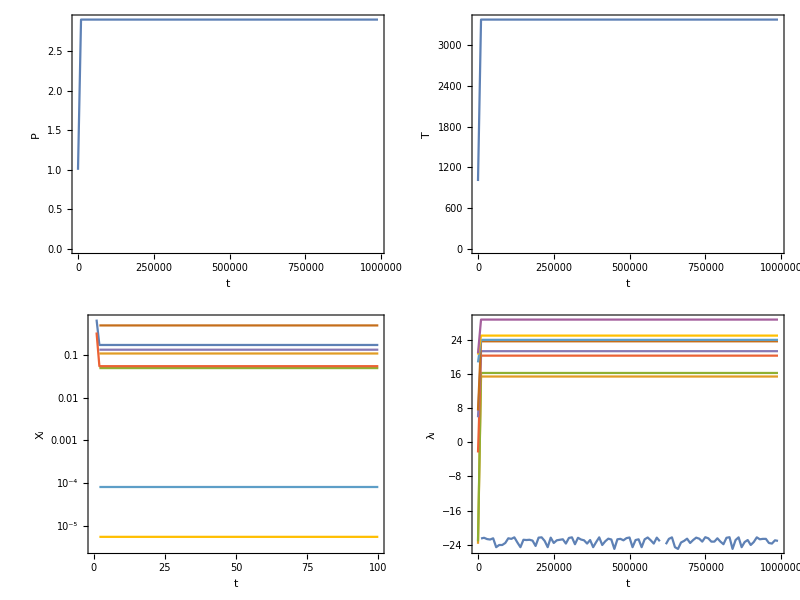

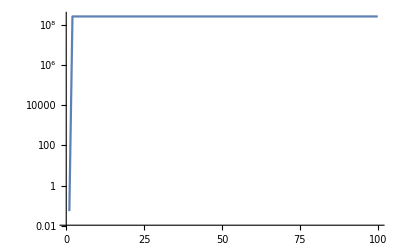

```mathematica
filebase="test"
dat=Import[filebase<>"out.dat"];
{Nt,ns,nr}=dat[[1,1;;3]]
A=Partition[Partition[BinaryReadList[filebase<>"matrices.npy","Real64"][[17;;-1]],ns],ns];
evals=Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvalues.npy","Real64"][[17;;-1]],2],ns];
evecs=Partition[Partition[#[[1]]+I*#[[2]]&/@Partition[BinaryReadList[filebase<>"eigenvectors.npy","Real64"][[17;;-1]],2],ns],ns];
concentrations=Partition[BinaryReadList[filebase<>"concentrations.npy","Real64"][[17;;-1]],Round[Nt]];
Grid[{{ListPlot[Transpose[{dat[[3]]/10^-3,dat[[5]]}],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{t, P}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,5}},AspectRatio->1],ListPlot[Transpose[{dat[[3]]/10^-3,dat[[4]]}],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{t, T}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,5}},AspectRatio->1]},{ListLogPlot[concentrations,Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{t, Subscript[X,i]}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,5}},AspectRatio->1],ListPlot[Transpose[{dat[[3]]/10^-3,#}]&/@Transpose[Log[Abs[evals]]],Frame->True, Axes->False,FrameStyle->Directive[AbsoluteThickness[2.0],Black],LabelStyle->Directive[16,Black],FrameLabel->{t, Subscript[λ,i]}, ImageSize->300, Joined->True,PlotRange->All,ImagePadding->{{75,15},{75,5}},AspectRatio->1]}}]
Manipulate[MatrixPlot[A[[m]]],{m,1,Length[A],1}]
ListLogPlot[Table[Norm[A[[m]].concentrations[[All,m]]],{m,1,Length[A]}],PlotRange->All,Joined->True]
```

```mathematica
A[[2]]
A[[-1]]
```

{{-6.1602×10^9,9.87878×10^9,-8.72966×10^9,-6.17847×10^6,-1.4483×10^9,1.28539×10^9,3.64072×10^9,6.84368×10^9,0.},{6.1564×10^9,-1.10295×10^10,9.77421×10^9,-1.64354×10^9,1.6251×10^9,-1.35109×10^9,-2.78957×10^9,-7.47271×10^9,-3.01351×10^6},{-2.51725×10^9,4.45962×10^9,-1.49492×10^10,9.69163×10^8,6.64484×10^9,-5.14198×10^8,-3.91598×10^8,-2.97154×10^9,0.},{-1.975×10^6,-8.28727×10^8,1.0886×10^9,-1.73056×10^9,4.30614×10^8,-7.5818×10^7,6.64766×10^10,-8.41775×10^7,-3.01351×10^6},{-1.12263×10^9,1.99976×10^9,1.2789×10^10,1.04419×10^9,-1.25328×10^10,1.82863×10^9,1.49112×10^11,-2.80217×10^12,0.},{3.63988×10^9,-5.47371×10^9,-5.10194×10^9,-7.81172×10^7,8.87511×10^9,-1.82871×10^9,-1.3973×10^11,2.8064×10^12,0.},{1.74983×10^6,3.34453×10^8,-652712.,7.67942×10^8,9.75534×10^7,4.36174×10^7,-2.67859×10^11,2.81567×10^12,3.01351×10^6},{225169.,-389031.,-339056.,-8664.19,-1.18942×10^8,3.22727×10^7,1.92754×10^11,-2.8163×10^12,0.},{0.,0.,0.,0.,0.,0.,0.,0.,-1.67347×10^-10}}

{{-6.1602×10^9,9.87878×10^9,-8.72966×10^9,-6.17847×10^6,-1.4483×10^9,1.28539×10^9,3.64072×10^9,6.84368×10^9,0.},{6.1564×10^9,-1.10295×10^10,9.77421×10^9,-1.64354×10^9,1.6251×10^9,-1.35109×10^9,-2.78957×10^9,-7.47271×10^9,-3.01351×10^6},{-2.51725×10^9,4.45962×10^9,-1.49492×10^10,9.69163×10^8,6.64484×10^9,-5.14198×10^8,-3.91598×10^8,-2.97154×10^9,0.},{-1.975×10^6,-8.28727×10^8,1.0886×10^9,-1.73056×10^9,4.30614×10^8,-7.5818×10^7,6.64766×10^10,-8.41775×10^7,-3.01351×10^6},{-1.12263×10^9,1.99976×10^9,1.2789×10^10,1.04419×10^9,-1.25328×10^10,1.82863×10^9,1.49112×10^11,-2.80217×10^12,0.},{3.63988×10^9,-5.47371×10^9,-5.10194×10^9,-7.81172×10^7,8.87511×10^9,-1.82871×10^9,-1.3973×10^11,2.8064×10^12,0.},{1.74983×10^6,3.34453×10^8,-652712.,7.67942×10^8,9.75534×10^7,4.36174×10^7,-2.67859×10^11,2.81567×10^12,3.01351×10^6},{225169.,-389031.,-339056.,-8664.19,-1.18942×10^8,3.22727×10^7,1.92754×10^11,-2.8163×10^12,0.},{0.,0.,0.,0.,0.,0.,0.,0.,9.45874×10^-11}}

```mathematica
A[[-1]].concentrations[[All,-1]]
```

{2.0564×10^7,-1.92042×10^8,-3.48378×10^6,-1.04853×10^8,-5.79427×10^7,6.07284×10^7,1.05964×10^8,5.94184×10^-7,0.}